```mathematica
(*No Poke Rectangle Old Method*)
```

```mathematica
vxy= 1/2 * (ty-tx-zy+zx)*(ty-tx+zy-zx)
θxy = ((1/2)*(ty-tx-zy-zx))^2
f=Exp[-ρ*vxy]
g=Exp[-ρ*(vxy-θxy)]
```

```mathematica
XREGION1O=(t (t √ρ-√2 DawsonF[(t √ρ)/(√2)]))/(2 ρ^(3/2))
```

```mathematica
(*Regiony1*)
y1=Integrate[Integrate[f,{zy,zx-(ty-tx),zx+(ty-tx)}],{ty,tx,tx + zx},Assumptions-> t>0&& ρ>0&&zx>=0&&tx>=0&&zx+tx<=t]
```

```mathematica
(*Regiony2*)
f;
(*Apply O^ Operator*)
%+2*ρ*D[%,ρ]+(ρ^2/2)*D[%,{ρ,2}];
Integrate[%,{zy,ty-tx-zx,ty-tx+zx},Assumptions-> t>0&& ρ>0&&zx>=0&&tx>=0&&zx+tx<=t];
y2O=Integrate[%,{ty,tx+zx, t},Assumptions-> t>0&& ρ>0&&zx>=0&&tx>=0&&zx+tx<=t]
```

```mathematica
y2O=1/(16 ρ)ⅇ^(-1/2 (t^2-2 t tx+zx^2) ρ) (4 ⅇ^(1/2 (t^2-2 t tx+zx^2) ρ)-4 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ)+2 ⅇ^(1/2 (t^2-2 t tx+zx^2) ρ) t^2 ρ-2 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) t^2 ρ-4 ⅇ^(1/2 (t^2-2 t tx+zx^2) ρ) t tx ρ+4 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) t tx ρ+2 ⅇ^(1/2 (t^2-2 t tx+zx^2) ρ) tx^2 ρ-2 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) tx^2 ρ+12 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) t zx ρ-12 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) tx zx ρ-4 ⅇ^(1/2 (t^2-2 t tx+zx^2) ρ) zx^2 ρ-8 ⅇ^(1/2 (t^2-2 t (tx+2 zx)+zx (4 tx+5 zx)) ρ) zx^2 ρ-ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) (-t+tx) √ρ (-3+t^2 ρ-2 t tx ρ+tx^2 ρ) Erfi[((-t+tx) √ρ)/(√2)]+2 ⅇ^(1/2 t (t-2 tx) ρ) √(2 π) zx √ρ (-3+zx^2 ρ) Erfi[(zx √ρ)/(√2)]+3 ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) t √ρ Erfi[((-t+tx+2 zx) √ρ)/(√2)]-3 ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) tx √ρ Erfi[((-t+tx+2 zx) √ρ)/(√2)]-ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) t^3 ρ^(3/2) Erfi[((-t+tx+2 zx) √ρ)/(√2)]+3 ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) t^2 tx ρ^(3/2) Erfi[((-t+tx+2 zx) √ρ)/(√2)]-3 ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) t tx^2 ρ^(3/2) Erfi[((-t+tx+2 zx) √ρ)/(√2)]+ⅇ^(1/2 (-tx+zx) (tx+zx) ρ) √(2 π) tx^3 ρ^(3/2) Erfi[((-t+tx+2 zx) √ρ)/(√2)])
```

```mathematica
(*Regiony3*)
g;
(*Apply O^ Operator*)
%+2*ρ*D[%,ρ]+(ρ^2/2)*D[%,{ρ,2}];
innery3O= Integrate[%,{zy,0,ty-tx-zx},Assumptions-> t>0&& ρ>0&&zx>=0&&tx>=0&&zx+tx<=t]
(*OUTERY3O CANT BE DONE ANALYTICALLY*)
(*outery3=Integrate[%,{ty,tx+zx, t},Assumptions-> t>0&& ρ>0&&zx>=0&&tx>=0&&zx+tx<=t]*)
```

```mathematica
innery3O=1/(432 √ρ)ⅇ^(-1/12 (5 tx^2+5 ty^2+10 ty zx-7 zx^2-8 tx (ty+zx)) ρ) (3 ⅇ^(1/6 (tx^2-tx (ty+zx)+(ty+zx)^2) ρ) (tx-ty-zx) √ρ (-30+7 tx^2 ρ+7 ty^2 ρ+14 ty zx ρ-17 zx^2 ρ-14 tx (ty+zx) ρ)+12 ⅇ^(1/12 (5 tx^2+5 ty^2-8 tx (ty-2 zx)-14 ty zx+17 zx^2) ρ) (tx-ty+2 zx) √ρ (-15+2 tx^2 ρ+2 ty^2 ρ+16 ty zx ρ-16 zx^2 ρ-4 tx (ty+4 zx) ρ)+2 ⅇ^(1/12 (tx^2+(ty+zx)^2) ρ) √(3 π) (27-36 ty^2 ρ+72 zx^2 ρ+4 tx^4 ρ^2+4 ty^4 ρ^2+16 ty^3 zx ρ^2+16 zx^4 ρ^2-16 tx^3 (ty+zx) ρ^2+12 tx^2 ρ (-3+2 ty^2 ρ+4 ty zx ρ)-8 tx (ty+zx) ρ (-9+2 ty^2 ρ+4 ty zx ρ-4 zx^2 ρ)-8 ty zx ρ (9+4 zx^2 ρ)) Erfi[((-tx+ty-2 zx) √ρ)/(√3)]-2 ⅇ^(1/12 (tx^2+(ty+zx)^2) ρ) √(3 π) (27-36 ty^2 ρ+72 zx^2 ρ+4 tx^4 ρ^2+4 ty^4 ρ^2+16 ty^3 zx ρ^2+16 zx^4 ρ^2-16 tx^3 (ty+zx) ρ^2+12 tx^2 ρ (-3+2 ty^2 ρ+4 ty zx ρ)-8 tx (ty+zx) ρ (-9+2 ty^2 ρ+4 ty zx ρ-4 zx^2 ρ)-8 ty zx ρ (9+4 zx^2 ρ)) Erfi[((tx-ty-zx) √ρ)/(2 √3)])
```

```mathematica
(*X INTEGRAL*)
Integrate[Integrate[y1,{zx,0,t-tx},Assumptions->t>0&&ρ>0&&zx>=0&&tx>=0&&zx+tx<=t],{tx,0,t},Assumptions->t>0&&ρ>0&&zx>=0&&tx>=0&&zx+tx<=t];
(*Apply O^ Operator*)
%+2*ρ*D[%,ρ]+(ρ^2/2)*D[%,{ρ,2}];
Result1O = %
```

```mathematica
Result1O=1/12 t^4 HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2]-(t^2 (-6+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]+t^2 ρ HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2]))/(6 ρ)+1/24 t^4 ρ^2 ((2 (-6+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]+t^2 ρ HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2]))/(t^2 ρ^3)-((6 ((ⅇ^(-(t^2 ρ)/2) √(π/2) Erfi[(t √ρ)/(√2)])/(t √ρ)-HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]))/ρ+t^2 HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2]-(-6+6 HypergeometricPFQ[{1,1},{3/2,2},-(t^2 ρ)/2]+t^2 ρ HypergeometricPFQ[{1,1},{5/2,3},-(t^2 ρ)/2])/ρ)/(t^2 ρ^2))
```

```mathematica
(*(*MUST DO X NUMERICALLY FOR y2O*)
y20/.t->1
%/.ρ->30
NIntegrate[%,{zx,0,t-tx},{tx,0,t}]
(*MUST DO OUTERY3O and X NUMERICALLY*)
innery30/.t->1
%/.ρ->30
NIntegrate[%,{ty,tx+zx, t},{zx,0,t-tx},{tx,0,t}]*)
```

```mathematica
ty2O=y2O/.t->1;
tResult1O=Result1O/.t->1;
tXREGION1O=XREGION1O/.t->1;
tinnery3O=innery3O/.t->1
```

```mathematica
(*tXREGION1O + 2(tResult1O+NIntegrate[ty2O,{zx,0,t-tx},{tx,0,t}]+NIntegrate[tinner3O,{zy,0,ty-tx-zx},{zx,0,t-tx},{tx,0,t}])*)
DistributeDefinitions[tXREGION1O,tResult1O,ty2O,tinnery3O];

DOULBENOPOKETABLE=ParallelTable[{ρ,2*FullSimplify[ρ*1*2-2 ρ^2*(tXREGION1O+2 (tResult1O+TimeConstrained[NIntegrate[ty2O,{tx,0,1},{zx,0,1-tx}],40]+TimeConstrained[NIntegrate[tinnery3O,{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}],40]))]},{ρ,1,30,1}];

ListLinePlot[DOULBENOPOKETABLE,PlotLabel->"Mean action numeric as a function of rho",AxesLabel->{"rho","Mean Action"}]
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O/.ρ->10)+2 ((tResult1O/.ρ->10)+NIntegrate[(ty2O/.ρ->10),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->10),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))]
%/.ρ->10
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O/.ρ->15.5)+2 ((tResult1O/.ρ->15.5)+NIntegrate[(ty2O/.ρ->15.5),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->15.5),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))]
%/.ρ->15.5
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->30),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->30),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))]
%/.ρ->30
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O/.ρ->40)+2 ((tResult1O/.ρ->40)+NIntegrate[(ty2O/.ρ->40),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->40),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))]
%/.ρ->40
```

2 (2-0.047293 ρ) ρ

8.66224

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->50),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->50),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))];
%/.ρ->50
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->80),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->80),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))];
%/.ρ->80
```

12.3874

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->100),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->100),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))];
%/.ρ->100
```

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->150),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->150),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))];
%/.ρ->150
```

17.0169

```mathematica
2*FullSimplify[ρ*1*2-2 ρ^2*((tXREGION1O)+2 ((tResult1O)+NIntegrate[(ty2O/.ρ->300),{tx,0,1},{zx,0,1-tx}]+NIntegrate[(tinnery3O/.ρ->300),{tx,0,1},{zx,0,1-tx},{ty,tx+zx,1}]))];
%/.ρ->300
```

```mathematica
data={{300,24.0956586}};
(*Define the model*)
model=c* Sqrt[ρ];

(*Fit the model to the data*)
fit=FindFit[data,model,{c},ρ]

(*Print the result*)
fit
```

```mathematica
(*Example data*)data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565}};
(*Define the model with the exponential decay term*)
model=a Sqrt[rho]+b Exp[-c rho];

(*Fit the model to the data*)
fit=FindFit[data,model,{a,b,c},rho]

(*Extract the a parameter*)
asymptoticValue=a/. fit
```

{a→1.37701,b→6.63239×10^6,c→666217.}

1.37701

```mathematica
(*Example data*)data={{100,13.8707710350},{150,17.016885299833},{300,24.09565}};
(*Define the model with the exponential decay term*)
model=a Sqrt[rho]+b Exp[-c rho];

(*Fit the model to the data*)
fit=FindFit[data,model,{a,b,c},rho]

(*Extract the a parameter*)
asymptoticValue=a/. fit
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindFit::nrlnum: The function value {Overflow[],Overflow[],Overflow[]} is not a list of real numbers with dimensions {3} at {a,b,c} = {1.39058,-4.45779×10^46,-4.45769×10^44}.

{a→1.39058,b→-4.45779×10^46,c→-4.45769×10^44}

1.39058

```mathematica
data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565},{400,27.82925357210353},{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}};
(*Define the model*)
model=c* Sqrt[ρ];

(*Fit the model to the data*)
fit=FindFit[data,model,{c},ρ]

(*Print the result*)
fit
```

{c→1.38826}

{c→1.38826}

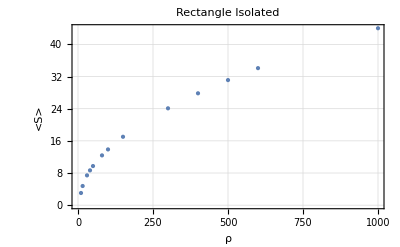

```mathematica
data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565},{400,27.82925357210353},{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}};

ListPlot[data,PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"ρ","<S>"},PlotLabel->"Rectangle Isolated",GridLines->Automatic]
```

{{500,31.1182},{600,34.0919},{1000,44.0154}}

{c→1.3918}

{c→1.3918}

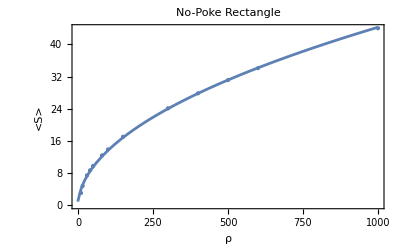

```mathematica
data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565},{400,27.82925357210353},{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}};
smalldata={{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}}
(*Define the model*)
model=c* Sqrt[ρ];

(*Fit the model to the data*)
fit=FindFit[smalldata,model,{c},ρ]

(*Print the result*)
a=fit
(*Define the predicted behavior function*)
predictedBehavior[x_]:=a* Sqrt[x]

(*Fit a linear model to the data*)
linearModel=LinearModelFit[data,{Sqrt[x]+Exp[-x],1},x];

Show[ListPlot[data,PlotStyle->PointSize[Medium],Frame->True,FrameLabel->{"ρ","<S>"},PlotLabel->"No-Poke Rectangle"],Plot[{linearModel[x],predictedBehavior[x]},{x,0,1000}]]
```

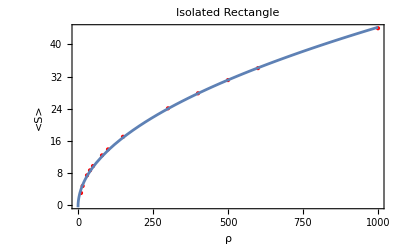

```mathematica
data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565},{400,27.82925357210353},{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}};

Show[ListPlot[data,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{"ρ","<S>"},PlotLabel->"Isolated Rectangle"],Plot[{linearModel[x],predictedBehavior[x]},{x,0,1000}]]
```

```mathematica
data={{10,3.031311},{15.5,4.771318},{30,7.4147171},{40,8.6622444459},{50,9.7350866},{80,12.3874088},{100,13.8707710350},{150,17.016885299833},{300,24.09565},{400,27.82925357210353},{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}};
smalldata={{500,31.1182165287196},{600,34.091873341347},{1000,44.01539026212322}}
(*Define the model*)
model=c* Sqrt[ρ];

(*Fit the model to the data*)
fit=FindFit[smalldata,model,{c},ρ]

(*Print the result*)
a=fit
(*Define the predicted behavior function*)
predictedBehavior[x_]:=a* Sqrt[x]

(*Fit a linear model to the data*)
linearModel=LinearModelFit[data,{Sqrt[x],1},x];
```

{{500,31.1182},{600,34.0919},{1000,44.0154}}

{c→1.3918}

{c→1.3918}